## Verify and Plot

```mathematica
ClearAll["Global`*"]
SetDirectory[NotebookDirectory[]];
getRegionSAS[sas_]:=And@@(GreaterEqual[#,0]&/@sas);
verifyResults[benchmark_,plot_,plotRange_,verifyTimeLimit_]:= Module[
{systemPath,xvarSet,yvarSet,zvarSet,s1,s2,hPath,hData,h,hHomo,sdpTime,verifyTime,totalTime,result,flag,flagHomo,flagNP,hNP,i},
systemPath=FileNameJoin[{".","Results","problem",StringJoin[benchmark,".txt"]}];
{xvarSet,yvarSet,zvarSet,s1,s2} = ReadList[systemPath];
(*Print["x Variables: ",xvarSet];Print["y Variables: ",yvarSet];Print["z Variables: ",zvarSet];
Print["S1: ",s1];
Print["S2: ",s2];
*)
Print[Style["Verifying results (CAV20 method)...", Blue]];
flag =1;
hPath=FileNameJoin[{".","Results","sufficient",StringJoin[benchmark,".txt"]}];
hData=ReadList[hPath,{Expression,Expression},RecordSeparators-> "\n"];

(*Length(hData)== 1 if the degree of the template is fixed*)
h = hData[[1]][[1]];
Print["candidate: ",h];
sdpTime = hData[[1]][[2]];
result=Timing[TimeConstrained[myVerify[xvarSet, yvarSet, zvarSet, s1,s2,h],verifyTimeLimit,2]];
verifyTime=result[[1]];
totalTime = sdpTime+verifyTime;
If[result[[2]]== 0,
Print[Style["Numerical Errors Detected.",Red]];
flag=0;
];
If[result[[2]]== 1,
Print[Style["Valid solution.",Green]];
Print["h",h]
];
If[result[[2]]== 2,
Print[Style["Verify out of time.",Red]];
Print[h]
];
Print["SDP Time: ",sdpTime ];
Print["verify Time: ",verifyTime ];
Print["Total Time: ",totalTime ];

Print[Style["Verifying results (homogenization)...", Blue]];
hPath=FileNameJoin[{".","Results","homo",StringJoin[benchmark,".txt"]}];
hData=ReadList[hPath,{Expression,Expression},RecordSeparators-> "\n"];
flagHomo=1;
(*Length(hData)== 1 if the degree of the template is fixed*)
hHomo = hData[[1]][[1]];
Print["candidate: ",hHomo];
sdpTime = hData[[1]][[2]];
result=Timing[TimeConstrained[myVerifyHomo[xvarSet, yvarSet, zvarSet, s1,s2,hHomo],verifyTimeLimit,2]];
verifyTime=result[[1]];
totalTime = sdpTime+verifyTime;
If[result[[2]]== 0,
Print[Style["Numerical Errors Detected.",Red]];
flagHomo=0
];
If[result[[2]]== 1,
Print[Style["Valid solution.",Green]];
Print["hHomo:",hHomo]
];
If[result[[2]]== 2,
Print[Style["Verify out of time.",Red]];
Print[hHomo]
];
Print["SDP Time: ",sdpTime ];
Print["verify Time: ",verifyTime ];
Print["Total Time: ",totalTime ];


Print[Style["Verifying results (Non-polynomial)...", Blue]];
hPath=FileNameJoin[{".","Results","nonpoly",StringJoin[benchmark,".txt"]}]; 
hData=ReadList[hPath,{Expression,Expression},RecordSeparators-> "\n"];
flagNP=1;
(*Length(hData)== 1 if the degree of the template is fixed*)
(*hNP = ReplaceAll[hData[[1]][[1]],w->Sqrt[Total[xvarSet^2]+1]];*)
hNP = hData[[1]][[1]];
Print["candidate: ",hNP];
sdpTime = hData[[1]][[2]];
result=Timing[TimeConstrained[myVerifyNP[xvarSet, yvarSet, zvarSet, s1,s2,hNP],verifyTimeLimit,2]];
verifyTime=result[[1]];
totalTime = sdpTime+verifyTime;
If[result[[2]]== 0,
Print[Style["Numerical Errors Detected.",Red]];
flagNP=0
];
If[result[[2]]== 1,
Print[Style["Valid solution.",Green]];
Print["hNP:",hNP]
];
If[result[[2]]== 2,
Print[Style["Verify out of time.",Red]];
Print[hNP]
];
Print["SDP Time: ",sdpTime ];
Print["verify Time: ",verifyTime ];
Print["Total Time: ",totalTime ];

If[ plot== 1,
(*If[Length[xvarSet]== 2,myPlot2D[xvarSet,yvarSet,zvarSet,plotRange,s1,s2,If[flag== 0,-1,h],If[flagHomo== 0,-1,hHomo]]];*)
If[Length[xvarSet]== 2,myPlot2D[xvarSet,yvarSet,zvarSet,plotRange,s1,s2,If[flag== 0,-1,h],If[flagHomo== 0,-1,hHomo], If[flagNP== 0,-1,hNP]]];
If[Length[xvarSet]== 3,myPlot3D[xvarSet,yvarSet,zvarSet,plotRange,s1,s2,If[flag== 0,-1,h],If[flagHomo== 0,-1,hHomo], If[flagNP== 0,-1,hNP]]];
]
]

myVerify [xvarSet_,yvarSet_,zvarSet_,s1_,s2_,h_]:= Module[
{lambda,s1Cons,s2Cons,bcLie,cond1,cond2,timev},
timev=Now;
s1Cons = Or@@(getRegionSAS[#]&/@s1);
s2Cons = Or@@(getRegionSAS[#]&/@s2);
cond1 = FindInstance[h-1< 0&&s1Cons,Join[xvarSet,yvarSet],Reals];
cond2 =FindInstance[-h-1<0&&s2Cons,Join[xvarSet,zvarSet],Reals];
Print["counter example: ",cond1,cond2];
If[Length[cond1]+Length[cond2]==0, (*no counter-example is found*)
Return[1],
Return[0]];
]
myVerifyHomo [xvarSet_,yvarSet_,zvarSet_,s1_,s2_,hHomo_]:= Module[
{lambda,s1Cons,s2Cons,bcLie,cond1,cond2,timev},
timev=Now;
s1Cons = Or@@(getRegionSAS[#]&/@s1);
s2Cons = Or@@(getRegionSAS[#]&/@s2);
cond1 = FindInstance[hHomo≤  0&&s1Cons,Join[xvarSet,yvarSet],Reals];
cond2 =FindInstance[-hHomo≤  0&&s2Cons,Join[xvarSet,zvarSet],Reals];
Print["counter example: ",cond1,cond2];
If[Length[cond1]+Length[cond2]==0, (*no counter-example is found*)
Return[1],
Return[0]];
]
myVerifyNP [xvarSet_,yvarSet_,zvarSet_,s1_,s2_,hHomo_]:= Module[
{lambda,s1Cons,s2Cons,bcLie,cond1,cond2,timev},
timev=Now;
s1Cons = Or@@(getRegionSAS[#]&/@s1);
s2Cons = Or@@(getRegionSAS[#]&/@s2);
cond1 = FindInstance[hHomo≤  0&&s1Cons&&w>= 0&&w^2== Total[xvarSet^2],Join[xvarSet,yvarSet,{w}],Reals];
cond2 =FindInstance[-hHomo≤  0&&s2Cons&&w>= 0&&w^2== Total[xvarSet^2],Join[xvarSet,zvarSet,{w}],Reals];
Print["counter example: ",cond1,cond2];
If[Length[cond1]+Length[cond2]==0, (*no counter-example is found*)
Return[1],
Return[0]];
]
myPlot2D [xvarSet_,yvarSet_,zvarSet_,xvarRange_,s1_,s2_,h_,hHomo_,hNP_]:= Module[
{ranges,s1Cons,s2Cons,s1Plot,s2Plot,hPlot,hHomoPlot,hNPPlot},
Print["Plot2d..."];
ranges=Sequence @@ MapThread[Prepend,{xvarRange,xvarSet}];
s1Cons = Or@@(getRegionSAS[#]&/@s1);
s2Cons = Or@@(getRegionSAS[#]&/@s2);
Print[s1Cons];
Print[s2Cons];
Print[h];
Print[hHomo];
(*s1Cons=And@@Thread[GreaterEqualThan[0][s1]];s2Cons=And@@Thread[GreaterEqualThan[0][s2]];*)
s1Plot=RegionPlot[Resolve[Exists[yvarSet,s1Cons],Reals],Evaluate[ranges],PlotStyle->{Opacity[0.65],RGBColor[0.28026441037696703, 0.715, 0.4292089322474965]},BoundaryStyle->None ,PlotPoints-> 100];
s2Plot=RegionPlot[Resolve[Exists[zvarSet,s2Cons],Reals],Evaluate[ranges],PlotStyle->{Opacity[0.65],RGBColor[0.915, 0.3325, 0.2125]},BoundaryStyle->None,PlotPoints-> 100];

hPlot=RegionPlot[h-1≥  0,Evaluate[ranges],PlotStyle->{Opacity[0.15],RGBColor[1, 0.75, 0]},BoundaryStyle-> {RGBColor[1, 0.75, 0]},PlotPoints-> 100];
hHomoPlot=RegionPlot[hHomo≥ 0,Evaluate[ranges],PlotStyle->{Opacity[0.15],RGBColor[0.363898, 0.618501, 0.782349]},BoundaryStyle->{RGBColor[0.363898, 0.618501, 0.782349]},PlotPoints-> 100];
hNPPlot=RegionPlot[ ReplaceAll[hNP,w-> Sqrt[Total[xvarSet^2]]]≥ 0,Evaluate[ranges],PlotStyle->{Opacity[0.15],RGBColor[0.363898, 0.618501, 0.782349]},BoundaryStyle-> {RGBColor[0.363898, 0.618501, 0.782349]},PlotPoints-> 100];
Print[Show[s1Plot,s2Plot,hPlot,(*hHomoPlot, *)hNPPlot, FrameLabel->xvarSet]]
]


(*inefficient, use other tools*)
myPlot3D [xvarSet_,yvarSet_,zvarSet_,xvarRange_,s1_,s2_,h_,hHomo_, hNP_]:= Module[
{ranges,s1Cons,s2Cons,s1Plot,s2Plot,hPlot,hHomoPlot},
Print["Plot3D..."];
ranges=Sequence @@ MapThread[Prepend,{xvarRange,xvarSet}];
ranges=Sequence @@ MapThread[Prepend,{xvarRange,xvarSet}];
s1Cons = Or@@(getRegionSAS[#]&/@s1);
s2Cons = Or@@(getRegionSAS[#]&/@s2);
s1Plot=RegionPlot3D[Resolve[Exists[yvarSet,s1Cons],Reals],Evaluate[ranges],PlotStyle->{Opacity[0.65],RGBColor[0.28026441037696703, 0.715, 0.4292089322474965]},BoundaryStyle->None ,PlotPoints-> 100];
s2Plot=RegionPlot3D[Resolve[Exists[zvarSet,s2Cons],Reals],Evaluate[ranges],PlotStyle->{Opacity[0.65],RGBColor[0.915, 0.3325, 0.2125]},BoundaryStyle->None,PlotPoints-> 100];
hPlot=RegionPlot3D[h-1≥  0,Evaluate[ranges],PlotStyle->{Opacity[0.15],RGBColor[1, 0.75, 0]},BoundaryStyle-> {RGBColor[1, 0.75, 0]},PlotPoints-> 100];
hHomoPlot=RegionPlot3D[hHomo≥ 0,Evaluate[ranges],PlotStyle->{Opacity[0.15],RGBColor[0.363898, 0.618501, 0.782349]},BoundaryStyle->{RGBColor[0.363898, 0.618501, 0.782349]},PlotPoints-> 100];
Print[Show[s1Plot,s2Plot,hPlot,hHomoPlot, FrameLabel->xvarSet]]
];
```

## Benchmarks

Benchmark:ex4

Verifying results (CAV20 method)...

candidate: -0.0600411+0.00931223 x+0.105602 x^2-0.000206843 x^3-0.00882141 y+x y+0.0313633 x^2 y+0.0796672 y^2+0.013075 x y^2+0.0330255 y^3

counter example: {{x→-0.543475,y→-1.}}{{x→0.596424,y→-1.}}

Numerical Errors Detected.

SDP Time: 0.0399293

verify Time: 0.010926

Total Time: 0.0508553

Verifying results (homogenization)...

candidate: -0.356214+0.0494608 x+0.35884 x^2-0.00690332 x^3+0.0188931 y+x y+0.0201597 x^2 y+0.310613 y^2-0.0365422 x y^2+0.0164385 y^3

counter example: {{x→134.,y→26.2}}{{x→1.5,y→-0.333333}}

Numerical Errors Detected.

SDP Time: 0.0473568

verify Time: 0.126718

Total Time: 0.174075

Verifying results (Non-polynomial)...

candidate: -0.0440221+0.0564432 w+0.0144644 x+0.0240726 w x-0.322531 x^2+0.231998 w x^2-0.0370346 x^3-0.000931842 y-0.0130518 w y+x y-0.0133326 w x y+0.0514931 x^2 y-0.281644 y^2+0.203557 w y^2-0.038443 x y^2+0.0389595 y^3

counter example: {}{}

Valid solution.

hNP:-0.0440221+0.0564432 w+0.0144644 x+0.0240726 w x-0.322531 x^2+0.231998 w x^2-0.0370346 x^3-0.000931842 y-0.0130518 w y+x y-0.0133326 w x y+0.0514931 x^2 y-0.281644 y^2+0.203557 w y^2-0.038443 x y^2+0.0389595 y^3

SDP Time: 0.183995

verify Time: 0.920565

Total Time: 1.10456

Plot2d...

-x^4+8. x y+2. x^2 y^3-y^6≥0&&-1.+x^2+y^2≥0

-x^4-12.5 x y-2. x^2 y^2-y^4≥0&&-1.+x^2+y^2≥0

-1

-1

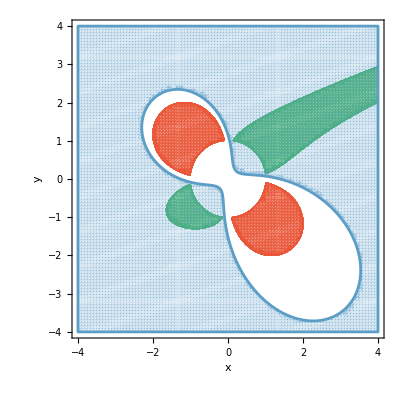

```mathematica
benchmarkname = "ex4";
Print["Benchmark:",benchmarkname];
verifytimelimit=10; (*verification time limit*)
plot =1; (*whether to plot(=1) or not (=0), better choose 2D examples*)
plotRange = {{-4,4},{-4,4}}; (*range for plot*)
verifyResults[benchmarkname,plot,plotRange,verifytimelimit];
```